```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Various parameters *)
Ωγ=2.469 10^-5 h^-2;Neff=3.04;h=0.704;
Ωr=Ωγ(1+0.2271 Neff);
Mpc=3.085677 *10^22;
cH0=0.925063 *10^26;
(cH0/Mpc)/√(.13)
(* Definition of R in terms of N=Log[a] *)
Ra[Nn_]:=6(2 H[Nn]^2+H[Nn] H'[Nn])
(* Definition of the f(R) Lagrangian  *)
f[R_]:=R-2Λ (1- 1/((1+(R/(b Λ))^2)^n))
n=1;
```

8314.75

```mathematica
Limit[f[R],b->0]
Limit[f[R],b->∞]
```

R-2 Λ

R

```mathematica
(* Definition of the ODE in terms of N=Log[a]=-Log[1+z] *)
ODE=-f'[R]H[Nn]^2+HL[Nn]^2-H0^2(1-om-or)+0(om Exp[-3 Nn]+or Exp[-4 Nn])+1/6(f'[R]R-f[R])-f''[R]H[Nn]^2 Ra'[Nn]/.Λ->3H0^2(1-om-or)/.R->Ra[Nn]//Simplify;
```

```mathematica
H[Nn_]:=√(HL[Nn]^2+Sum[b^(2i) Subscript[δH, 2i][Nn],{i,1,2}])
```

```mathematica
s0=Series[ODE,{b,0,4}]//Simplify
```

1/4 (-12 δH_2[Nn]-(2 H0^6 (-1+om+or)^3)/(HL[Nn] (2 HL[Nn]+HL'[Nn])^3)+(3 H0^6 (-1+om+or)^3)/(HL[Nn]^2 (2 HL[Nn]+HL'[Nn])^2)+(2 δH_2[Nn] (2 HL[Nn]+HL'[Nn]))/HL[Nn]+δH_2[Nn] (4-(2 HL'[Nn])/HL[Nn])+(6 H0^6 (-1+om+or)^3 (HL'[Nn]^2+HL[Nn] (4 HL'[Nn]+HL''[Nn])))/(HL[Nn]^2 (2 HL[Nn]+HL'[Nn])^4)) b^2+1/16 (-48 δH_4[Nn]-(8 H0^6 (-1+om+or)^3 δH_2[Nn])/(HL[Nn]^3 (2 HL[Nn]+HL'[Nn])^3)-(2 (δH_2[Nn]^2-4 HL[Nn]^2 δH_4[Nn]) (2 HL[Nn]+HL'[Nn]))/HL[Nn]^3+(4 H0^6 (-1+om+or)^3 (4 δH_2[Nn]+δH_2'[Nn]))/(HL[Nn]^3 (2 HL[Nn]+HL'[Nn])^3)+(4 δH_2[Nn] (-δH_2[Nn] HL'[Nn]+HL[Nn] (2 δH_2[Nn]+δH_2'[Nn])))/HL[Nn]^3+(4 H0^6 (-1+om+or)^3 (H0^4 (-1+om+or)^2+6 HL[Nn]^2 (4 δH_2[Nn]+δH_2'[Nn])+3 HL[Nn] HL'[Nn] (4 δH_2[Nn]+δH_2'[Nn])))/(HL[Nn]^3 (2 HL[Nn]+HL'[Nn])^5)-(4 H0^6 (-1+om+or)^3 (H0^4 (-1+om+or)^2+6 HL[Nn]^2 (4 δH_2[Nn]+δH_2'[Nn])+3 HL[Nn] HL'[Nn] (4 δH_2[Nn]+δH_2'[Nn])))/(HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^4)-(H0^6 (-1+om+or)^3 (H0^4 (-1+om+or)^2+8 HL[Nn]^2 (4 δH_2[Nn]+δH_2'[Nn])+4 HL[Nn] HL'[Nn] (4 δH_2[Nn]+δH_2'[Nn])))/(HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^4)-8 δH_4'[Nn]+1/HL[Nn]^3(6 δH_2[Nn]^2 HL'[Nn]-8 HL[Nn]^2 δH_4[Nn] HL'[Nn]-4 HL[Nn] δH_2[Nn] (δH_2[Nn]+δH_2'[Nn])+8 HL[Nn]^3 (2 δH_4[Nn]+δH_4'[Nn]))-(4 H0^6 (-1+om+or)^3 (HL'[Nn]^2 (5 H0^4 (-1+om+or)^2-6 δH_2[Nn] HL'[Nn]^2)+HL[Nn] (20 H0^4 (-1+om+or)^2 HL'[Nn]+12 HL'[Nn]^3 δH_2'[Nn]+5 H0^4 (-1+om+or)^2 HL''[Nn]-6 δH_2[Nn] HL'[Nn]^2 HL''[Nn])+12 HL[Nn]^3 (2 δH_2'[Nn] HL''[Nn]+6 δH_2[Nn] (4 HL'[Nn]+HL''[Nn])+HL'[Nn] (4 δH_2'[Nn]-δH_2''[Nn]))+3 HL[Nn]^2 HL'[Nn] (4 δH_2'[Nn] HL''[Nn]+8 δH_2[Nn] (7 HL'[Nn]+HL''[Nn])+HL'[Nn] (20 δH_2'[Nn]-δH_2''[Nn]))-12 HL[Nn]^4 (4 δH_2'[Nn]+δH_2''[Nn])))/(HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^6)) b^4+O[b]^5

```mathematica
Solve[SeriesCoefficient[s0,2]==0,Subscript[δH, 2][Nn]]//FullSimplify
```

{{δH_2[Nn]→(H0^6 (-1+om+or)^3 (8 HL[Nn]^2+9 HL'[Nn]^2+HL[Nn] (34 HL'[Nn]+6 HL''[Nn])))/(4 HL[Nn]^2 (2 HL[Nn]+HL'[Nn])^4)}}

```mathematica
Subscript[δH, 2][Nn_]:=(H0^6 (-1+om+or)^3 (8 HL[Nn]^2+9 HL'[Nn]^2+HL[Nn] (34 HL'[Nn]+6 HL''[Nn])))/(4 HL[Nn]^2 (2 HL[Nn]+HL'[Nn])^4)
```

```mathematica
Solve[SeriesCoefficient[s0,4]==0,Subscript[δH, 4][Nn]]//FullSimplify
```

{{δH_4[Nn]→-(H0^10 (-1+om+or)^5 (192 HL[Nn]^8-486 H0^2 (-1+om+or) HL'[Nn]^6+320 HL[Nn]^7 (6 HL'[Nn]+HL''[Nn])-18 H0^2 (-1+om+or) HL[Nn] HL'[Nn]^4 (263 HL'[Nn]+48 HL''[Nn])+16 HL[Nn]^6 (32 H0^2 (-1+om+or)+5 HL'[Nn] (47 HL'[Nn]+8 HL''[Nn]))+HL[Nn]^2 HL'[Nn]^2 (-15562 H0^2 (-1+om+or) HL'[Nn]^2+25 HL'[Nn]^4-972 H0^2 (-1+om+or) HL''[Nn]^2-12 H0^2 (-1+om+or) HL'[Nn] (532 HL''[Nn]-15 HL^(3)[Nn]))+4 HL[Nn]^4 (4422 H0^2 (-1+om+or) HL'[Nn]^2+345 HL'[Nn]^4+40 HL'[Nn]^3 HL''[Nn]+72 H0^2 (-1+om+or) HL''[Nn] (9 HL''[Nn]+2 HL^(3)[Nn])+18 H0^2 (-1+om+or) HL'[Nn] (175 HL''[Nn]+20 HL^(3)[Nn]-HL^(4)[Nn]))-2 HL[Nn]^3 (7000 H0^2 (-1+om+or) HL'[Nn]^3-148 HL'[Nn]^5-10 HL'[Nn]^4 HL''[Nn]+324 H0^2 (-1+om+or) HL''[Nn]^3+36 H0^2 (-1+om+or) HL'[Nn] HL''[Nn] (63 HL''[Nn]-4 HL^(3)[Nn])+9 H0^2 (-1+om+or) HL'[Nn]^2 (609 HL''[Nn]-66 HL^(3)[Nn]+HL^(4)[Nn]))+8 HL[Nn]^5 (824 H0^2 (-1+om+or) HL'[Nn]+400 HL'[Nn]^3+60 HL'[Nn]^2 HL''[Nn]+3 H0^2 (-1+om+or) (29 HL''[Nn]-3 (6 HL^(3)[Nn]+HL^(4)[Nn])))))/(16 HL[Nn]^6 (2 HL[Nn]+HL'[Nn])^10)}}

```mathematica
Subscript[δH, 4][Nn_]:=-(H0^10 (-1+om+or)^5 (192 HL[Nn]^8-486 H0^2 (-1+om+or) HL'[Nn]^6+320 HL[Nn]^7 (6 HL'[Nn]+HL''[Nn])-18 H0^2 (-1+om+or) HL[Nn] HL'[Nn]^4 (263 HL'[Nn]+48 HL''[Nn])+16 HL[Nn]^6 (32 H0^2 (-1+om+or)+5 HL'[Nn] (47 HL'[Nn]+8 HL''[Nn]))+HL[Nn]^2 HL'[Nn]^2 (-15562 H0^2 (-1+om+or) HL'[Nn]^2+25 HL'[Nn]^4-972 H0^2 (-1+om+or) HL''[Nn]^2-12 H0^2 (-1+om+or) HL'[Nn] (532 HL''[Nn]-15 Derivative[3][HL][Nn]))+4 HL[Nn]^4 (4422 H0^2 (-1+om+or) HL'[Nn]^2+345 HL'[Nn]^4+40 HL'[Nn]^3 HL''[Nn]+72 H0^2 (-1+om+or) HL''[Nn] (9 HL''[Nn]+2 Derivative[3][HL][Nn])+18 H0^2 (-1+om+or) HL'[Nn] (175 HL''[Nn]+20 Derivative[3][HL][Nn]-Derivative[4][HL][Nn]))-2 HL[Nn]^3 (7000 H0^2 (-1+om+or) HL'[Nn]^3-148 HL'[Nn]^5-10 HL'[Nn]^4 HL''[Nn]+324 H0^2 (-1+om+or) HL''[Nn]^3+36 H0^2 (-1+om+or) HL'[Nn] HL''[Nn] (63 HL''[Nn]-4 Derivative[3][HL][Nn])+9 H0^2 (-1+om+or) HL'[Nn]^2 (609 HL''[Nn]-66 Derivative[3][HL][Nn]+Derivative[4][HL][Nn]))+8 HL[Nn]^5 (824 H0^2 (-1+om+or) HL'[Nn]+400 HL'[Nn]^3+60 HL'[Nn]^2 HL''[Nn]+3 H0^2 (-1+om+or) (29 HL''[Nn]-3 (6 Derivative[3][HL][Nn]+Derivative[4][HL][Nn])))))/(16 HL[Nn]^6 (2 HL[Nn]+HL'[Nn])^10)
```

```mathematica
HL[Nn_]:=√((om Exp[-3 Nn]+or Exp[-4 Nn])+(1-om-or))
```

```mathematica
hh=H[Nn]//Simplify
```

√(1-om+ⅇ^(-3 Nn) om-or+ⅇ^(-4 Nn) or+(b^2 ⅇ^(5 Nn) H0^6 (-1+om+or)^3 (-37 ⅇ^Nn om^2-40 om or+32 ⅇ^(4 Nn) om (-1+om+or)+16 ⅇ^(3 Nn) or (-1+om+or)+32 ⅇ^(7 Nn) (-1+om+or)^2))/(om-4 ⅇ^(3 Nn) (-1+om+or))^4+(b^4 ⅇ^(11 Nn) H0^10 (-1+om+or)^5 (123 ⅇ^Nn om^6+128 om^5 or-4 ⅇ^(4 Nn) (522+20165 H0^2) om^5 (-1+om+or)-40 ⅇ^(3 Nn) (52+3959 H0^2) om^4 or (-1+om+or)-77760 ⅇ^(2 Nn) H0^2 om^3 or^2 (-1+om+or)-8 ⅇ^(7 Nn) (-1710+7279 H0^2) om^4 (-1+om+or)^2-64 ⅇ^(6 Nn) (-200+4537 H0^2) om^3 or (-1+om+or)^2-228096 ⅇ^(5 Nn) H0^2 om^2 or^2 (-1+om+or)^2+256 ⅇ^(10 Nn) (-165+1294 H0^2) om^3 (-1+om+or)^3+128 ⅇ^(9 Nn) (-280+2703 H0^2) om^2 or (-1+om+or)^3-82944 ⅇ^(8 Nn) H0^2 om or^2 (-1+om+or)^3-640 ⅇ^(13 Nn) (-90+457 H0^2) om^2 (-1+om+or)^4-2048 ⅇ^(12 Nn) (-20+23 H0^2) om or (-1+om+or)^4+2048 ⅇ^(16 Nn) (-9+40 H0^2) om (-1+om+or)^5+4096 ⅇ^(15 Nn) (-2+7 H0^2) or (-1+om+or)^5+4096 ⅇ^(19 Nn) (-3+8 H0^2) (-1+om+or)^6))/(om-4 ⅇ^(3 Nn) (-1+om+or))^10)

```mathematica
H0=1;
Happrox[Nn_,b_,om_]:=√(1-om+ⅇ^(-3 Nn) om-or+ⅇ^(-4 Nn) or+(b^2 ⅇ^(5 Nn) H0^6 (-1+om+or)^3 (-37 ⅇ^Nn om^2-40 om or+32 ⅇ^(4 Nn) om (-1+om+or)+16 ⅇ^(3 Nn) or (-1+om+or)+32 ⅇ^(7 Nn) (-1+om+or)^2))/(om-4 ⅇ^(3 Nn) (-1+om+or))^4+(b^4 ⅇ^(11 Nn) H0^10 (-1+om+or)^5 (123 ⅇ^Nn om^6+128 om^5 or-4 ⅇ^(4 Nn) (522+20165 H0^2) om^5 (-1+om+or)-40 ⅇ^(3 Nn) (52+3959 H0^2) om^4 or (-1+om+or)-77760 ⅇ^(2 Nn) H0^2 om^3 or^2 (-1+om+or)-8 ⅇ^(7 Nn) (-1710+7279 H0^2) om^4 (-1+om+or)^2-64 ⅇ^(6 Nn) (-200+4537 H0^2) om^3 or (-1+om+or)^2-228096 ⅇ^(5 Nn) H0^2 om^2 or^2 (-1+om+or)^2+256 ⅇ^(10 Nn) (-165+1294 H0^2) om^3 (-1+om+or)^3+128 ⅇ^(9 Nn) (-280+2703 H0^2) om^2 or (-1+om+or)^3-82944 ⅇ^(8 Nn) H0^2 om or^2 (-1+om+or)^3-640 ⅇ^(13 Nn) (-90+457 H0^2) om^2 (-1+om+or)^4-2048 ⅇ^(12 Nn) (-20+23 H0^2) om or (-1+om+or)^4+2048 ⅇ^(16 Nn) (-9+40 H0^2) om (-1+om+or)^5+4096 ⅇ^(15 Nn) (-2+7 H0^2) or (-1+om+or)^5+4096 ⅇ^(19 Nn) (-3+8 H0^2) (-1+om+or)^6))/(om-4 ⅇ^(3 Nn) (-1+om+or))^10)/.or->Ωr
```

```mathematica
(* Solve the ODE *)
h=0.704;
or0=Ωr;
om0=.24;
Clear[H]
H0=1;
modfried[om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(modfried[om1,b1,Ns]=NDSolve[{(ODE/.om->om1/.b->b1/.or->or0//Evaluate)==0,H[Ns]==√(om0 Exp[-3 Ns]+or0 Exp[-4 Ns]+1-om0-or0),H'[Ns]==-(ⅇ^(-4 Ns) (3 ⅇ^Ns om0+4 or0))/(2 √(1+(-1+ⅇ^(-3 Ns)) om0+(-1+ⅇ^(-4 Ns)) or0))},H,{Nn,Ns,0},MaxSteps->2000000])
Hsol[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H[Nn]/.modfried[om1,b1,Ns][[1]])
Hsolp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H'[Nn]/.modfried[om1,b1,Ns][[1]])
yH[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((H[Nn]^2/om0-Exp[-3Nn]-or0/om0 Exp[-4Nn])/.modfried[om1,b1,Ns][[1]])
yHp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((3 ⅇ^(-3 Nn)+(4 ⅇ^(-4 Nn) or0)/om0+(2 H[Nn] H'[Nn])/om0)/.modfried[om1,b1,Ns][[1]])
```

```mathematica
Ns=Log[1/(1+20.)];
```

```mathematica
100(1-Happrox[Log[1/(1+0.1)],0.05,om0]/Hsol[Log[1/(1+0.1)],om0,.05,Ns])
```

-8.90559×10^-7

```mathematica
100(1-Happrox[Log[1/(1+0.1)],0.1,om0]/Hsol[Log[1/(1+0.1)],om0,.1,Ns])
```

1.7795×10^-7

```mathematica
100(1-Happrox[Log[1/(1+0.1)],0.5,om0]/Hsol[Log[1/(1+0.1)],om0,.5,Ns])
```

0.0237155

```mathematica
100(1-Happrox[Log[1/(1+0.1)],1,om0]/Hsol[Log[1/(1+0.1)],om0,1,Ns])
```

0.752046

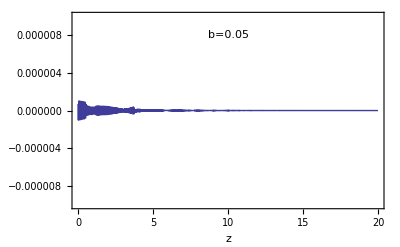

```mathematica
Plot[100(1-Happrox[Log[1/(1+z)],0.05,om0]/Hsol[Log[1/(1+z)],om0,.05,Ns]),{z,0.,20.},PlotRange->{-.00001,.00001},Frame->True,FrameLabel->{"z","% diff from NDSOLVE"},Epilog->{Text["b=0.05",{10,0.000008}]}]
```

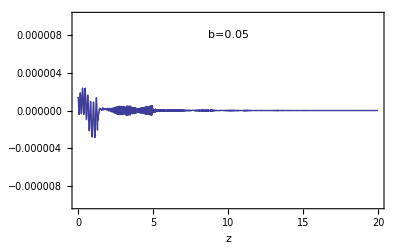

```mathematica
Plot[100(1-Happrox[Log[1/(1+z)],0.1,om0]/Hsol[Log[1/(1+z)],om0,0.1,Ns]),{z,0.,20.},PlotRange->{-.00001,.00001},Frame->True,FrameLabel->{"z","% diff from NDSOLVE"},Epilog->{Text["b=0.05",{10,0.000008}]}]
```

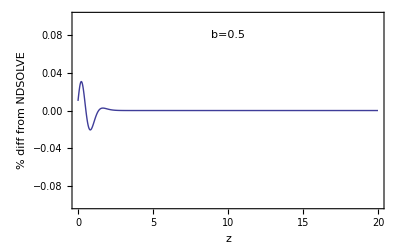

```mathematica
Plot[100(1-Happrox[Log[1/(1+z)],0.5,om0]/Hsol[Log[1/(1+z)],om0,.5,Ns]),{z,0.,20.},PlotRange->{-0.1,0.1},Frame->True,FrameLabel->{"z","% diff from NDSOLVE"},Epilog->{Text["b=0.5",{10,0.08}]}]
```

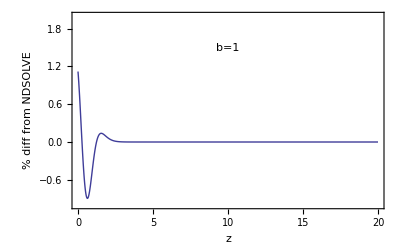

```mathematica
Plot[100(1-Happrox[Log[1/(1+z)],1,om0]/Hsol[Log[1/(1+z)],om0,1,Ns]),{z,0.,20.},PlotRange->{-1,2},Frame->True,FrameLabel->{"z","% diff from NDSOLVE"},Epilog->{Text["b=1",{10,1.5}]}]
```

```mathematica
Off[NIntegrate::slwcon,NIntegrate::ncvb]
```

```mathematica
{Hsol[Log[1/(1+0.1)],om0,.05,Ns],Hsol[Log[1/(1+0.1)],om0,.075,Ns],Hsol[Log[1/(1+0.1)],om0,.1,Ns],Hsol[Log[1/(1+0.1)],om0,.25,Ns],Hsol[Log[1/(1+0.1)],om0,.3,Ns],Hsol[Log[1/(1+0.1)],om0,.4,Ns],Hsol[Log[1/(1+0.1)],om0,.5,Ns],Hsol[Log[1/(1+0.1)],om0,.75,Ns],Hsol[Log[1/(1+0.1)],om0,1,Ns],Hsol[Log[1/(1+0.1)],om0,2,Ns]}
```

{1.03895,1.03892,1.03887,1.0383,1.03802,1.0374,1.03691,1.03844,1.04425,1.07622}

```mathematica
testdatH=Table[{b,NIntegrate[100*(1-Happrox[Log[1/(1+z)],b,0.24]/Hsol[Log[1/(1+z)],om0,b,Ns]),{z,0,20}]/20//Abs},{b,{0.05,0.075,0.1,0.25,0.3,0.4,0.5,0.75,1,2}}];
```

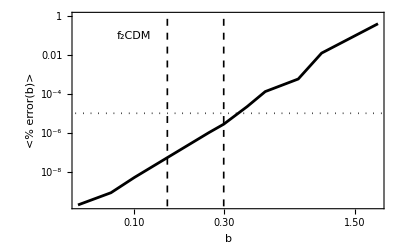

```mathematica
pl2=ListLogLogPlot[testdatH,Frame->True,Joined->True,PlotStyle->{Thickness[0.005],Black},FrameLabel->{"b","<% error(b)>"},BaseStyle->{FontSize->18,FontFamily->"Times"},Epilog->{{Dashed,Thickness[0.003],Line[{{0.15,10^-15},{0.15,2}}//Log]},{Dashed,Thickness[0.003],Line[{{0.3,10^-15},{0.3,2}}//Log]},{Dotted,Thickness[0.003],Line[{{0.001,10^-5},{10,10^-5}}//Log]},Text["f_2CDM",Log[{0.1,0.1}]]},PlotRangeClipping->True]
```

```mathematica
Export[".\\plots\\accuracyH(z)_Starob.eps",pl2,ImageSize->600]
```

.\plots\accuracyH(z)_Starob.eps